## (1+1)D Code Test

## Setup

### working directory

```mathematica
wd=SetDirectory@NotebookDirectory[]
root=ParentDirectory[wd]
filedir="/Users/Lipei/Documents/GitHub/BEShydro/output"
outputDir=filedir;
```

/Users/Lipei/Documents/GitHub/BEShydro/tests/Plotting

/Users/Lipei/Documents/GitHub/BEShydro/tests

/Users/Lipei/Documents/GitHub/BEShydro/output

### plot styles

```mathematica
FrameTicksFontSize=22;
FrameFontSize=22;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[FontSize->FrameTicksFontSize,FontFamily->"Times",FontColor->Black],Directive[FontSize->FrameTicksFontSize,FontFamily->"Times",FontColor->Black]},FrameStyle->{Directive[AbsoluteThickness[1.1]],Directive[AbsoluteThickness[1.1]]},LabelStyle->{FontFamily->"Times",FontSize->FrameFontSize,FontColor->Black},BaseStyle->{FontFamily->"Times",FontSize->FrameFontSize,FontColor->Black},AspectRatio->2.5/3,ImageSize->300,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[ListLinePlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];
SetOptions[ListLogPlot,PlotOptions];
SetOptions[ParametricPlot,PlotOptions];
SetOptions[ContourPlot,PlotOptions];
SetOptions[ListDensityPlot,PlotOptions];
SetOptions[DensityPlot,PlotOptions];
```

## System setup

### equation of state

```mathematica
hbarc=0.197326938;
fac=16/Pi^2;
P[e_]=e/3;
Tint[e_,n_]=1/3*e/n;
muT[e_,n_]=(Log[27/fac]+4*Log[n]-3*Log[e]);
kappaBeta[n_]=n/12;
tauInv[n_]=4n/9;
s[e_,n_]=(e+P[e])/Tint[e,n]-muT[e,n]*n;
```

### initial condition

```mathematica
R0=0.5;wid=100;n1=1.0;n2=-1.0;T0=0.5/hbarc;nmax=10;
ModG[x_]=Exp[-2wid*Sqrt[1+x^2/R0^2/wid]+2wid];
```

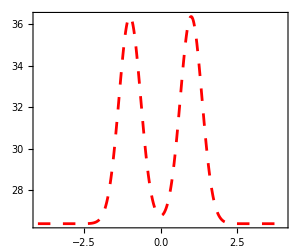

```mathematica
ndi[x_]=fac*T0^3+nmax*(ModG[x+n1]+ModG[x+n2]);
nplot=Plot[{ndi[x]},{x,-4,4},PlotRange->All,PlotStyle->{{AbsoluteThickness[2],Red,Dashing[Medium]},{AbsoluteThickness[1],Red,Dashing[Medium]}}]
```

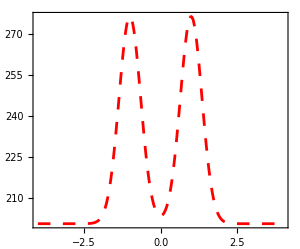

```mathematica
ei[x_]=3*T0*ndi[x];
eplot=Plot[ei[x],{x,-4,4},PlotRange->All,PlotStyle->{{AbsoluteThickness[2],Red,Dashing[Medium]},{AbsoluteThickness[2],Darker[Green],Dashing[Medium]}}]
```

## Longitudinal expansion

### setup

```mathematica
tlist={1,2,4,6};
clist={{AbsoluteThickness[1.5],Magenta,Dashing[Large]},{AbsoluteThickness[1.5],Red,Dashing[Large]},{AbsoluteThickness[1.5],Darker[Green],Dashing[Large]},{AbsoluteThickness[1.5],Blue,Dashing[Large]}};
clist1={Magenta,Red,Darker[Green],Blue};
```

```mathematica
t0=1.;
tf=20.;
```

```mathematica
nm=4;
```

```mathematica
impadding={{95,5},{53,5}};
impadding2={{95,5},{3,5}};
```

### equations of motion

```mathematica
Clear[ut,theta,edExact,ndExact,unExact,e,un,nd]
Offpaclet:ref/Off[NDSolve::bcart];
```

```mathematica
ut[t_,n_]=Sqrt[1+t*t*un[t,n]*un[t,n]];
theta[t_,n_]=ut[t,n]/t+D[ut[t,n],t]+D[un[t,n],n];
nt[t_,n_]=t*t*(un[t,n]*nn[t,n])/ut[t,n];
Dunu[t_,n_]=(1-ut[t,n]*ut[t,n])*D[nt[t,n],t]+(1-t*t*un[t,n]*un[t,n])*D[nn[t,n],n]+ut[t,n]*un[t,n]*(t*t*D[nn[t,n],t]-D[nt[t,n],n]);
```

```mathematica
eqs={ut[t,n]*D[e[t,n],t]+un[t,n]*D[e[t,n],n]==-(e[t,n]+P[e[t,n]])*theta[t,n],
ut[t,n]*D[nd[t,n],t]+un[t,n]*D[nd[t,n],n]==-nd[t,n]*theta[t,n]-Dunu[t,n],
(e[t,n]+P[e[t,n]])*(ut[t,n]*D[un[t,n],t]+un[t,n]*D[un[t,n],n]+2*(ut[t,n]*un[t,n])/t)==(-D[P[e[t,n]],n])/t^2-un[t,n]*(ut[t,n]*D[P[e[t,n]],t]+un[t,n]*D[P[e[t,n]],n]),
ut[t,n]*D[nn[t,n],t]+un[t,n]*D[nn[t,n],n]==-kappaBeta[nd[t,n]]*(1/t/t+un[t,n]*un[t,n])*D[muT[e[t,n],nd[t,n]],n]-kappaBeta[nd[t,n]]*ut[t,n]*un[t,n]*D[muT[e[t,n],nd[t,n]],t]-tauInv[nd[t,n]]*nn[t,n]-un[t,n]*nt[t,n](ut[t,n]*D[ut[t,n],t]+un[t,n]*D[ut[t,n],n]+t*un[t,n]*un[t,n])+t*t*un[t,n]*nn[t,n](ut[t,n]*D[un[t,n],t]+un[t,n]*D[un[t,n],n]+2*(ut[t,n]*un[t,n])/t)-(ut[t,n]*nn[t,n]+un[t,n]*nt[t,n])/t};
initcond={e[t0,n]==ei[n],nd[t0,n]==ndi[n],un[t0,n]==0.,nn[t0,n]==0};
{edExact,ndExact,unExact,nnExact}={e,nd,un,nn}/.NDSolve[Join[eqs,initcond],{e,nd,un,nn},{t,t0,tf},{n,-nm,nm}][[1]];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable n. Artificial boundary effects may be present in the solution.

### make plots

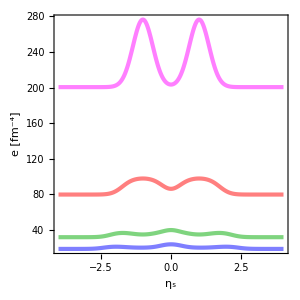

```mathematica
eplot=Show[Table[Plot[edExact[tlist[[i]],n],{n,-nm,nm},PlotRange->All,PlotStyle->{{AbsoluteThickness[3],clist1[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist1[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"η_s","e [fm^-4]"},AspectRatio->3./3,ImagePadding->impadding]
```

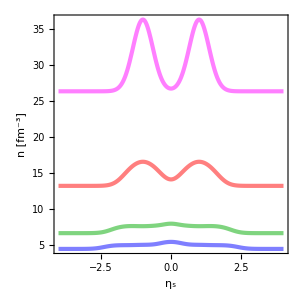

```mathematica
nplot=Show[Table[Plot[ndExact[tlist[[i]],n],{n,-nm,nm},PlotRange->All,PlotStyle->{{AbsoluteThickness[3],clist1[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist1[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"η_s","n [fm^-3]"},AspectRatio->3./3,ImagePadding->impadding2]
```

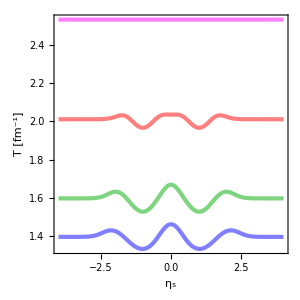

```mathematica
Tplot=Show[Table[Plot[Tint[edExact[tlist[[i]],n],ndExact[tlist[[i]],n]],{n,-nm,nm},PlotRange->All,PlotStyle->{{AbsoluteThickness[3],clist1[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"η_s","T [fm^-1]"},AspectRatio->3./3,ImagePadding->impadding]
```

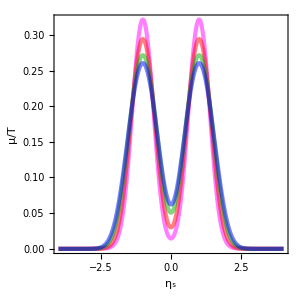

```mathematica
mutplot=Show[Table[Plot[muT[edExact[tlist[[i]],n],ndExact[tlist[[i]],n]],{n,-nm,nm},PlotRange->All,PlotStyle->{{AbsoluteThickness[3],clist1[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"η_s","μ/T"},AspectRatio->3./3,ImagePadding->impadding]
```

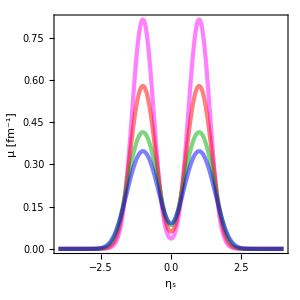

```mathematica
muplot=Show[Table[Plot[muT[edExact[tlist[[i]],n],ndExact[tlist[[i]],n]]*Tint[edExact[tlist[[i]],n],ndExact[tlist[[i]],n]],{n,-nm,nm},PlotRange->All,PlotStyle->{{AbsoluteThickness[3],clist1[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"η_s","μ [fm^-1]"},AspectRatio->3./3,ImagePadding->impadding2]
```

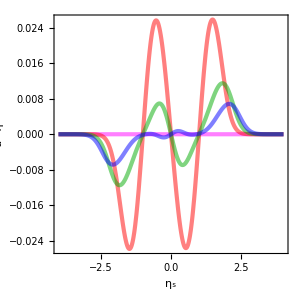

```mathematica
unplot=Show[Table[Plot[unExact[tlist[[i]],n],{n,-nm,nm},PlotRange->All,PlotStyle->{{AbsoluteThickness[3],clist1[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"η_s","u^η"},AspectRatio->3./3,ImagePadding->impadding]
```

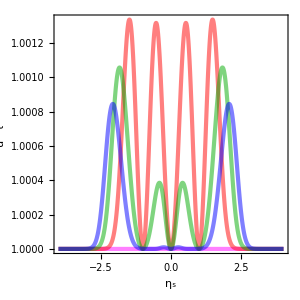

```mathematica
utplot=Show[Table[Plot[Sqrt[1+tlist[[i]]*tlist[[i]]*unExact[tlist[[i]],n]*unExact[tlist[[i]],n]],{n,-nm,nm},PlotRange->All,PlotStyle->{{AbsoluteThickness[3],clist1[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"η_s","u^τ"},AspectRatio->3./3,ImagePadding->impadding]
```

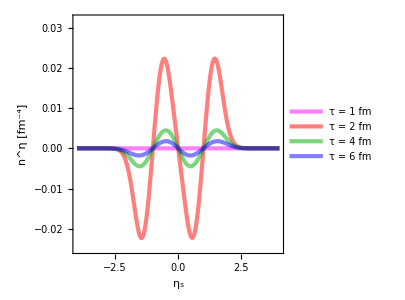

```mathematica
nnplot=Show[Table[Plot[nnExact[tlist[[i]],n],{n,-nm,nm},PlotRange->{All,{-0.025,0.032}},PlotStyle->{{AbsoluteThickness[3],clist1[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist[[i]],Dashed}},PlotLegends->Placed[LineLegend[{"τ = "<>ToString[PaddedForm[tlist[[i]],{2,1},NumberPadding->{"","0"}]]<>" fm"},LabelStyle-> {FontSize->12,FontFamily->"Times"},LegendMarkerSize->{{20,10}}],{0.2,1.02-0.1*i}]],{i,1,Length[tlist]}],FrameLabel->{"η_s","n^η [fm^-4]"},AspectRatio->3./3,ImagePadding->impadding]
```

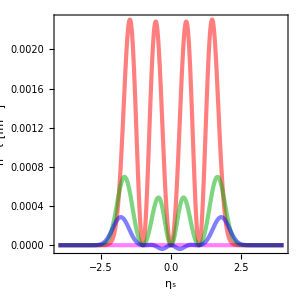

```mathematica
ntplot=Show[Table[Plot[tlist[[i]]*tlist[[i]]*unExact[tlist[[i]],n]*nnExact[tlist[[i]],n]/Sqrt[1-tlist[[i]]*tlist[[i]]*unExact[tlist[[i]],n]*unExact[tlist[[i]],n]],{n,-nm,nm},PlotRange->All,PlotStyle->{{AbsoluteThickness[3],clist1[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"η_s","n^τ [fm^-3]"},AspectRatio->3./3,ImagePadding->impadding]
```

### numerical solutions

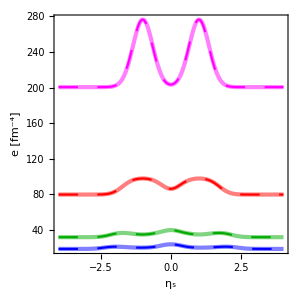

```mathematica
e1cdata=Import[filedir<>"/e_1.000.dat"];
e1c =e1cdata[[All,{3,4}]];
e2cdata=Import[filedir<>"/e_2.000.dat"];
e2c =e2cdata[[All,{3,4}]];
e3cdata=Import[filedir<>"/e_4.000.dat"];
e3c =e3cdata[[All,{3,4}]];
e4cdata=Import[filedir<>"/e_6.000.dat"];
e4c =e4cdata[[All,{3,4}]];
plot2=ListLinePlot[{e1c,e2c,e3c,e4c},PlotStyle->clist];
Show[eplot,plot2,PlotRange->{{-nm,nm},All}]
```

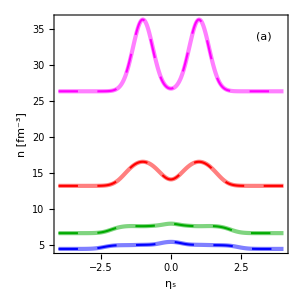

```mathematica
e1cdata=Import[filedir<>"/rhob_1.000.dat"];
e1c =e1cdata[[All,{3,4}]];
e2cdata=Import[filedir<>"/rhob_2.000.dat"];
e2c =e2cdata[[All,{3,4}]];
e3cdata=Import[filedir<>"/rhob_4.000.dat"];
e3c =e3cdata[[All,{3,4}]];
e4cdata=Import[filedir<>"/rhob_6.000.dat"];
e4c =e4cdata[[All,{3,4}]];
plot2=ListLinePlot[{e1c,e2c,e3c,e4c},PlotStyle->clist];
nPlot=Show[nplot,plot2,PlotRange->{{-nm,nm},All},Epilog->Inset["(a)",{3.3,34}]]
```

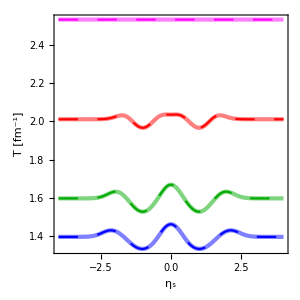

```mathematica
e1cdata=Import[filedir<>"/T_1.000.dat"];
e1c =e1cdata[[All,{3,4}]];
e2cdata=Import[filedir<>"/T_2.000.dat"];
e2c =e2cdata[[All,{3,4}]];
e3cdata=Import[filedir<>"/T_4.000.dat"];
e3c =e3cdata[[All,{3,4}]];
e4cdata=Import[filedir<>"/T_6.000.dat"];
e4c =e4cdata[[All,{3,4}]];
plot2=ListLinePlot[{e1c,e2c,e3c,e4c},PlotStyle->clist];
Show[Tplot,plot2,PlotRange->{{-nm,nm},All}]
```

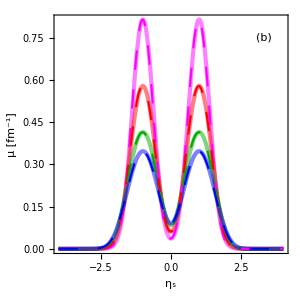

```mathematica
e1cdata=Import[filedir<>"/muBT_1.000.dat"];
e1c =e1cdata[[All,{3,4}]];
e2cdata=Import[filedir<>"/muBT_2.000.dat"];
e2c =e2cdata[[All,{3,4}]];
e3cdata=Import[filedir<>"/muBT_4.000.dat"];
e3c =e3cdata[[All,{3,4}]];
e4cdata=Import[filedir<>"/muBT_6.000.dat"];
e4c =e4cdata[[All,{3,4}]];
plot2=ListLinePlot[{e1c,e2c,e3c,e4c},PlotStyle->clist];
muPlot=Show[muplot,plot2,PlotRange->{{-nm,nm},All},Epilog->Inset["(b)",{3.3,0.75}]]
```

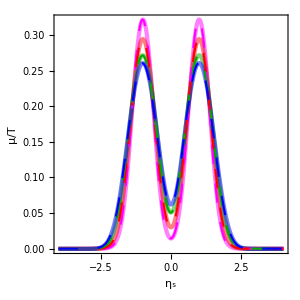

```mathematica
e1cdata=Import[filedir<>"/alphaB_1.000.dat"];
e1c =e1cdata[[All,{3,4}]];
e2cdata=Import[filedir<>"/alphaB_2.000.dat"];
e2c =e2cdata[[All,{3,4}]];
e3cdata=Import[filedir<>"/alphaB_4.000.dat"];
e3c =e3cdata[[All,{3,4}]];
e4cdata=Import[filedir<>"/alphaB_6.000.dat"];
e4c =e4cdata[[All,{3,4}]];
plot2=ListLinePlot[{e1c,e2c,e3c,e4c},PlotStyle->clist];
Show[mutplot,plot2,PlotRange->{{-nm,nm},All}]
```

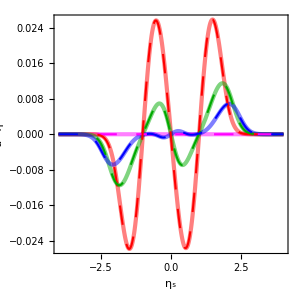

```mathematica
e1cdata=Import[filedir<>"/un_1.000.dat"];
e1c =e1cdata[[All,{3,4}]];
e2cdata=Import[filedir<>"/un_2.000.dat"];
e2c =e2cdata[[All,{3,4}]];
e3cdata=Import[filedir<>"/un_4.000.dat"];
e3c =e3cdata[[All,{3,4}]];
e4cdata=Import[filedir<>"/un_6.000.dat"];
e4c =e4cdata[[All,{3,4}]];
plot2=ListLinePlot[{e1c,e2c,e3c,e4c},PlotStyle->clist];
Show[unplot,plot2,PlotRange->{{-nm,nm},All}]
```

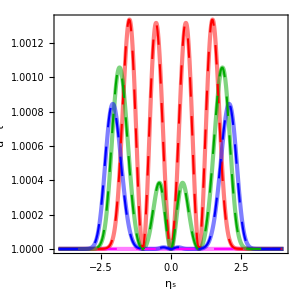

```mathematica
e1cdata=Import[filedir<>"/ut_1.000.dat"];
e1c =e1cdata[[All,{3,4}]];
e2cdata=Import[filedir<>"/ut_2.000.dat"];
e2c =e2cdata[[All,{3,4}]];
e3cdata=Import[filedir<>"/ut_4.000.dat"];
e3c =e3cdata[[All,{3,4}]];
e4cdata=Import[filedir<>"/ut_6.000.dat"];
e4c =e4cdata[[All,{3,4}]];
plot2=ListLinePlot[{e1c,e2c,e3c,e4c},PlotStyle->clist];
Show[utplot,plot2,PlotRange->{{-nm,nm},All}]
```

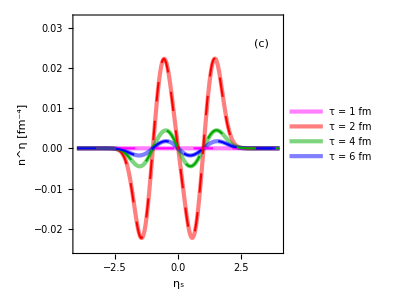

```mathematica
e1cdata=Import[filedir<>"/nbn_1.000.dat"];
e1c =e1cdata[[All,{3,4}]];
e2cdata=Import[filedir<>"/nbn_2.000.dat"];
e2c =e2cdata[[All,{3,4}]];
e3cdata=Import[filedir<>"/nbn_4.000.dat"];
e3c =e3cdata[[All,{3,4}]];
e4cdata=Import[filedir<>"/nbn_6.000.dat"];
e4c =e4cdata[[All,{3,4}]];
plot2=ListLinePlot[{e1c,e2c,e3c,e4c},PlotStyle->clist];
nnPlot=Show[nnplot,plot2,PlotRange->{{-nm,nm},{-0.025,0.032}},Epilog->Inset["(c)",{3.3,0.026}]]
```

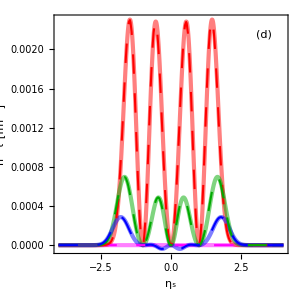

```mathematica
e1cdata=Import[filedir<>"/nbtau_1.000.dat"];
e1c =e1cdata[[All,{3,4}]];
e2cdata=Import[filedir<>"/nbtau_2.000.dat"];
e2c =e2cdata[[All,{3,4}]];
e3cdata=Import[filedir<>"/nbtau_4.000.dat"];
e3c =e3cdata[[All,{3,4}]];
e4cdata=Import[filedir<>"/nbtau_6.000.dat"];
e4c =e4cdata[[All,{3,4}]];
plot2=ListLinePlot[{e1c,e2c,e3c,e4c},PlotStyle->clist];
ntPlot=Show[ntplot,plot2,PlotRange->{{-nm,nm},All},Epilog->Inset["(d)",{3.3,0.00215}]]
```

### grid plots

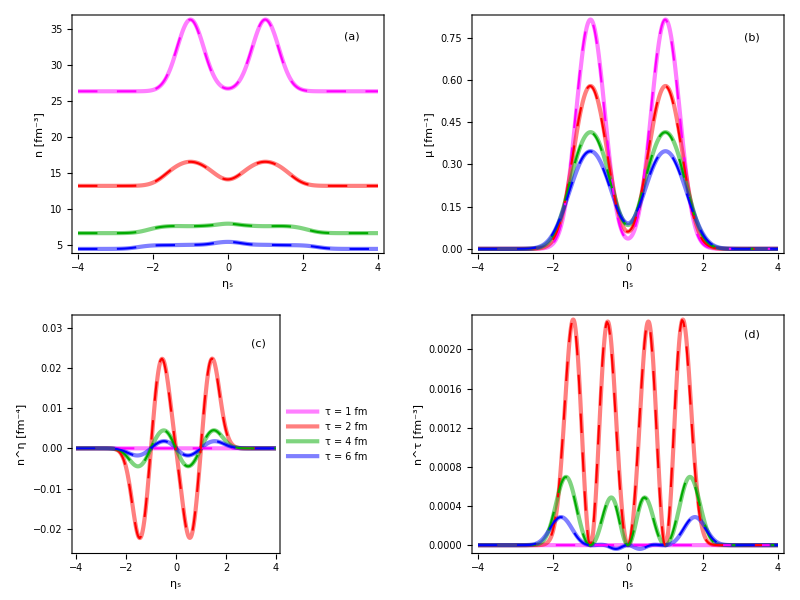

```mathematica
gPlot=Grid[{{nPlot,muPlot},{nnPlot,ntPlot}},Spacings->{0, 2}]
```

```mathematica
Export[wd<>"/diffusion_test.pdf",gPlot]
```

/Users/Lipei/Documents/Research/Notes/BEShydroTests/diffusion_test.pdf